```mathematica
fp[x_] = ap x +bp
fi[x_] = ai E^(bi x)+ci
fd[x_] = ad x +bd
```

bp+ap x

ci+ai ⅇ^(bi x)

bd+ad x

```mathematica
rp=Solve[{fp[0]==0.00025, fp[150]==0.00015},{ap, bp}];
ri=Solve[{fi[0]==0.00045, fi[150]==0.000001, fi[40]==0.0002},{ai, bi, ci}];
rd=Solve[{fd[0]==0.0005, fd[150]==0.00008},{ad, bd}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Kp[x_]=fp[x]/.rp[[1]]
Ki[x_]=fi[x]/.ri[[1]]
Kd[x_]=fd[x]/.rd[[1]]
```

0.00025-6.66667×10^-7 x

-0.0000291363+0.000479136 ⅇ^(-0.0184417 x)

0.0005-2.8×10^-6 x

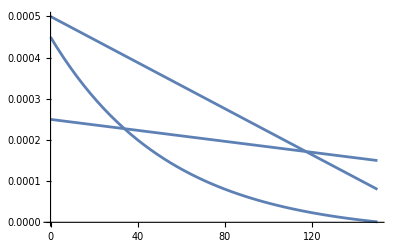

```mathematica
Show[
Plot[Kp[x], {x, 0, 150}, PlotRange->All, AxesOrigin->{0,0}],
Plot[Ki[x], {x, 0, 150}, PlotRange->All, AxesOrigin->{0,0}],
Plot[Kd[x], {x, 0, 150}, PlotRange->All, AxesOrigin->{0,0}]
]
```

```mathematica
Ki[0]
```

0.00045